## EJERCICIO 6 - Algoritmo de Gerla

## Rubén Ripa García

Aplicar el algoritmo de Gerla en la siguiente red donde los nodos vienen identificados mediante letras (A, B, C, D y E) y los enlaces mediante números (del 1 al 7). Para simplificar, los enlaces son unidireccionales.

-Graphics-

El tráfico de entrada consta únicamente de dos flujos que son: γ_AD = 2 paquetes/seg y γ_BE = 4 paquetes/seg. La longitud media de los paquetes es 1/μ’ = 1000 bits/paquete. Las capacidades de los enlaces son las siguientes (en bits/seg): C_1=C_3=C_6=5000 bps, C_2=C_4=C_5=C_7=10000 bps.

El vector de flujo inicial (f⃗)^(0) es igual a {2000, 0, 0, 4000, 0, 4000, 0}
El tráfico de AD va directamente de A a D y el tráfico de BE va de B a C y luego de C a E

```mathematica
Clear["Global`*"]
```

```mathematica
(* DATOS *)
γAD=2; (* Tráfico externo del flujo AD *)
γBE=4; (* Tráfico externo del flujo BE *)
μ=1/1000; (* Tasa de servicio (en paquetes/s) *)
l=1000; (* Valor medio de la longitud de los paquetes (en bits/paquete) *)
Nodos=5; (* Número de nodos *)
M=7; (* Número de enlaces *)

γjk={{0,0,0,2,0},{0,0,0,0,4},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}; (* Tráfico externo *)
γ=∑_(j=1)^Nodos ∑_(k=1)^Nodos γjk[[j]][[k]]; (* Tasa media total de paquetes externos (paq/seg) *)
Ci={5000,10000,5000,10000,10000,5000,10000}; (* Capacidad de los enlaces *)

λi={γAD,0,0,γBE,0,γBE,0}; (* Valor medio de la tasa de paquetes de los enlaces i (en paquetes/s) *)
```

```mathematica
Treal=∑_(i=1)^M 1/γ*λi[[i]]/(μ*Ci[[i]]-λi[[i]])//N
```

0.888889

## ITERACIÓN 1

## PASO 1

Tomar n = 0 -Graphics-

```mathematica
f0=λi/μ(* Vector de flujo inicial *)
```

{2000,0,0,4000,0,4000,0}

## PASO 2

Sensibilidad del retardo medio de tránsito al aumento en el flujo en dicho enlace     
Derivando parcialmente T respecto de f_i = λ_i / μ’ queda la siguiente fórmula -Graphics-

```mathematica
li=Ci/(γ*(Ci-f0)^2)
li//N
```

{1/10800,1/60000,1/30000,1/21600,1/60000,1/1200,1/60000}

{0.0000925926,0.0000166667,0.0000333333,0.0000462963,0.0000166667,0.000833333,0.0000166667}

## PASO 3

Calcular la tasa incremental de coste para el vector (f⃗)^(n) -Graphics-

```mathematica
β0=∑_(i=1)^M li[[i]]*f0[[i]]//N
```

3.7037

## PASO 4

Calcular las rutas más cortas entre cada par de nodos, utilizando como métrica la sensibilidad de los canales

```mathematica
(* Para el flujo AD, hay 3 posibilidades: AD, ACD, ABCD *)
liAD=li[[1]];
liACD=li[[2]]+li[[5]];
liABCD=li[[3]]+li[[4]]+li[[5]];
liFlujoAD={liAD,liACD,liABCD}//N
MinRutaAD=Min[liFlujoAD] (* La ruta más corta entre AD es la de ACD *)

(* Para el flujo BE, hay 2 posibilidades: BCE, BCDE *)
liBCE=li[[4]]+li[[6]];
liBCDE=li[[4]]+li[[5]]+li[[7]];
liFlujoBE={liBCE,liBCDE}//N
MinRutaBE=Min[liFlujoBE] (* La ruta más corta entre BE es la de BCDE *)
```

{0.0000925926,0.0000333333,0.0000962963}

0.0000333333

{0.00087963,0.0000796296}

0.0000796296

Calcular el vector de flujo resultante de utilizar las rutas más cortas. -Graphics-

```mathematica
λi={0,γAD,0,γBE,γAD+γBE,0,γBE};
ϕ=λi/μ
```

{0,2000,0,4000,6000,0,4000}

## PASO 5

Calcular la tasa incremental de coste para el flujo ϕ⃗ -Graphics-

```mathematica
b0=∑_(i=1)^M li[[i]]*ϕ[[i]]//N
```

0.385185

## PASO 6

Condición de parada del algoritmo:
  · Si β_n - b_n < ϵ donde ϵ > 0 → PARAR ((f⃗)^(n) es la solución)
  · Si no, ir al PASO 7

```mathematica
β0-b0
```

3.31852

Con este resultado, el valor de ϵ debería ser mayor a 3.31852 para que se cumpla la condición de parada del algoritmo, pero es bastante elevado. Por lo tanto, se va a realizar otra iteración para conseguir un valor de ϵ más pequeño y un resultado más preciso.

## PASO 7

Calcular α (0 ≤ α ≤ 1) tal que minimice T → -Graphics-

```mathematica
T[α_]=∑_(i=1)^M 1/γ*((1-α)*f0[[i]]+α*ϕ[[i]])/(Ci[[i]]-((1-α)*f0[[i]]+α*ϕ[[i]]));
```

```mathematica
(* FORMA 1: Derivando e igualando a cero para calcular los mínimos *)
dT=D[T[α],α];
αSol=NSolve[dT==0,α];
αMin=SelectFirst[α/. αSol,Element[#,Reals]&&0<=#<=1&]

(* FORMA 2: Obteniendo el valor de α que minimice el retardo medio T *)
αSol=NMinimize[{T[α],0<=α<=1},α,Method->"DifferentialEvolution",AccuracyGoal->10];
αMin=α/.αSol[[2]]
```

0.585623

0.585623

```mathematica
Treal0=T[αMin]//N
```

0.390255

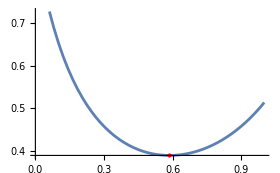

```mathematica
Plot[T[α],{α,0,1},Epilog->{Red,PointSize[Large],Point[{αMin,T[αMin]}]}]
```

## PASO 8

Desviación de flujo, donde el resultado de la asignación indica que parte del flujo es desviado por las rutas más cortas y el retardo medio de tránsito más bajo -Graphics-

```mathematica
f1=(1-αMin)*f0+αMin*ϕ
```

{828.754,1171.25,0.,4000.,3513.74,1657.51,2342.49}

## ITERACIÓN 2

## PASO 1

Tomar n = 1 -Graphics-

```mathematica
f1(* Vector de flujo 1 *)
```

{828.754,1171.25,0.,4000.,3513.74,1657.51,2342.49}

## PASO 2

Sensibilidad del retardo medio de tránsito al aumento en el flujo en dicho enlace     
Derivando parcialmente T respecto de f_i = λ_i / μ’ queda la siguiente fórmula -Graphics-

```mathematica
li=Ci/(γ*(Ci-f1)^2)
```

{0.0000478947,0.0000213821,0.0000333333,0.0000462963,0.000039615,0.0000745895,0.0000284233}

## PASO 3

Calcular la tasa incremental de coste para el vector (f⃗)^(n) -Graphics-

```mathematica
β1=∑_(i=1)^M li[[i]]*f1[[i]]
```

0.579333

## PASO 4

Calcular las rutas más cortas entre cada par de nodos, utilizando como métrica la sensibilidad de los canales

```mathematica
(* Para el flujo AD, hay 3 posibilidades: AD, ACD, ABCD *)
liAD=li[[1]];
liACD=li[[2]]+li[[5]];
liABCD=li[[3]]+li[[4]]+li[[5]];
liFlujoAD={liAD,liACD,liABCD}//N
MinRutaAD=Min[liFlujoAD] (* La ruta más corta entre AD es la de AD *)

(* Para el flujo BE, hay 2 posibilidades: BCE, BCDE *)
liBCE=li[[4]]+li[[6]];
liBCDE=li[[4]]+li[[5]]+li[[7]];
liFlujoBE={liBCE,liBCDE}//N
MinRutaBE=Min[liFlujoBE] (* La ruta más corta entre BE es la de BCDE *)
```

{0.0000478947,0.0000609971,0.000119245}

0.0000478947

{0.000120886,0.000114335}

0.000114335

Calcular el vector de flujo resultante de utilizar las rutas más cortas. -Graphics-

```mathematica
λi={γAD,0,0,γBE,γBE,0,γBE};
ϕ=λi/μ
```

{2000,0,0,4000,4000,0,4000}

## PASO 5

Calcular la tasa incremental de coste para el flujo ϕ⃗ -Graphics-

```mathematica
b1=∑_(i=1)^M li[[i]]*ϕ[[i]]//N
```

0.553128

## PASO 6

Condición de parada del algoritmo:
  · Si β_n - b_n < ϵ donde ϵ > 0 → PARAR ((f⃗)^(n) es la solución)
  · Si no, ir al PASO 7

```mathematica
β1-b1
```

0.0262049

Ahora, ya se ha obtenido un resultado .08muchísimo más pequeño en comparación con el de la primera iteración, por lo que en esta segunda iteración, el valor de ϵ debería ser mayor que 0.0262049 para que se cumpla la condición de parada del algoritmo. Este ya sería un resultado muy ACEPTABLE, pero se ha decidido realizar una última iteración.

## PASO 7

Calcular α (0 ≤ α ≤ 1) tal que minimice T → -Graphics-

```mathematica
T[α_]=∑_(i=1)^M (1/γ)*(((1-α)*f1[[i]]+α*ϕ[[i]])/(Ci[[i]]-((1-α)*f1[[i]]+α*ϕ[[i]])));
```

```mathematica
(* FORMA 1: Derivando e igualando a cero para calcular los mínimos *)
dT=D[T[α],α];
αSol=NSolve[dT==0,α];
αMin=SelectFirst[α/. αSol,Element[#,Reals]&&0<=#<=1&]

(* FORMA 2: Obteniendo el valor de α que minimice el retardo medio T *)
αSol=NMinimize[{T[α],0<=α<=1},α,Method->"DifferentialEvolution",AccuracyGoal->10];
αMin=α/.αSol[[2]]
```

0.150081

0.150081

```mathematica
Treal1=T[αMin]//N
```

0.388321

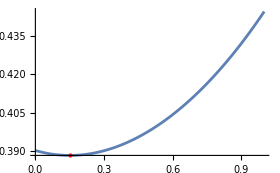

```mathematica
Plot[T[α],{α,0,1},Epilog->{Red,PointSize[Large],Point[{αMin,T[αMin]}]}]
```

## PASO 8

Desviación de flujo, donde el resultado de la asignación indica que parte del flujo es desviado por las rutas más cortas y el retardo medio de tránsito más bajo -Graphics-

```mathematica
f2=(1-αMin)*f1+αMin*ϕ
```

{1004.53,995.465,0.,4000.,3586.72,1408.75,2591.25}

## ITERACIÓN 3

## PASO 1

Tomar n = 2 -Graphics-

```mathematica
f2(* Vector de flujo 2 *)
```

{1004.53,995.465,0.,4000.,3586.72,1408.75,2591.25}

## PASO 2

Sensibilidad del retardo medio de tránsito al aumento en el flujo en dicho enlace     
Derivando parcialmente T respecto de f_i = λ_i / μ’ queda la siguiente fórmula -Graphics-

```mathematica
li=Ci/(γ*(Ci-f2)^2)
```

{0.0000522016,0.0000205554,0.0000333333,0.0000462963,0.0000405217,0.000064614,0.000030364}

## PASO 3

Calcular la tasa incremental de coste para el vector (f⃗)^(n) -Graphics-

```mathematica
β2=∑_(i=1)^M li[[i]]*f2[[i]]
```

0.573131

## PASO 4

Calcular las rutas más cortas entre cada par de nodos, utilizando como métrica la sensibilidad de los canales

```mathematica
(* Para el flujo AD, hay 3 posibilidades: AD, ACD, ABCD *)
liAD=li[[1]];
liACD=li[[2]]+li[[5]];
liABCD=li[[3]]+li[[4]]+li[[5]];
liFlujoAD={liAD,liACD,liABCD}//N
MinRutaAD=Min[liFlujoAD] (* La ruta más corta entre AD es la de AD *)

(* Para el flujo BE, hay 2 posibilidades: BCE, BCDE *)
liBCE=li[[4]]+li[[6]];
liBCDE=li[[4]]+li[[5]]+li[[7]];
liFlujoBE={liBCE,liBCDE}//N
MinRutaBE=Min[liFlujoBE] (* La ruta más corta entre BE es la de BCE *)
```

{0.0000522016,0.0000610771,0.000120151}

0.0000522016

{0.00011091,0.000117182}

0.00011091

Calcular el vector de flujo resultante de utilizar las rutas más cortas. -Graphics-

```mathematica
λi={γAD,0,0,γBE,0,γBE,0};
ϕ=λi/μ
```

{2000,0,0,4000,0,4000,0}

## PASO 5

Calcular la tasa incremental de coste para el flujo ϕ⃗ -Graphics-

```mathematica
b2=∑_(i=1)^M li[[i]]*ϕ[[i]]//N
```

0.548045

## PASO 6

Condición de parada del algoritmo:
  · Si β_n - b_n < ϵ donde ϵ > 0 → PARAR ((f⃗)^(n) es la solución)
  · Si no, ir al PASO 7

```mathematica
β2-b2
```

0.0250869

Por último, se puede comprobar que se ha obtenido un resultado similar al de la segunda iteración, pero ligeramente menor, por lo que ya si que se puede dar por bueno este resultado, con un ϵ que debería ser mayor a 0.0250869. La rutas más cortas y óptimos son:
  · Flujo γAD: Ruta óptima AD
  · Flujo γBE: Ruta óptima BCE
  
{1004.53, 995.465, 0., 4000., 3586.72, 1408.75, 2591.25}
{5000, 10000, 5000, 10000, 10000, 5000, 10000}

-Graphics--Graphics-

```mathematica
v1={1,0,0,1,0,1,0} (* AD y BCE *)
v2={1,0,0,1,1,0,1} (* AD y BCDE *)
v3={0,1,0,1,1,1,0} (* ACD y BCE *)
v4={0,1,0,1,1,0,1}(* ACD y BCDE *)
v5={0,0,1,1,1,1,0} (* ABCD y BCE *)
v6={0,0,1,1,1,0,1} (* ABCD y BCDE *)
```